```mathematica
(*problem solve the differentional equation where g is the gravitational acceleration  using the initional coditions t=0,y=h,t=0,y'=0*)
```

```mathematica
deq=y''[t]==g;
sol=DSolve[deq,y[t],t]
```

{{y[t]→(g t^2)/2+C[1]+t C[2]}}

```mathematica
yt=y[t]/.sol[[1]]
```

(g t^2)/2+C[1]+t C[2]

```mathematica
vt=D[yt,t]
```

g t+C[2]

```mathematica
yt=yt/.g->9.8
```

4.9 t^2+C[1]+t C[2]

```mathematica
vt=vt/.g->9.8
```

9.8 t+C[2]

```mathematica
eq1=(yt/.t->0)==5
eq2=(vt/.t->0)==0
```

C[1]==5

C[2]==0

```mathematica
constant=Solve[{eq1,eq2},{C[1],C[2]}]
```

{{C[1]→5,C[2]→0}}

```mathematica
yt=yt/.constant[[1]]
vt=vt/.constant[[1]]
```

5+4.9 t^2

9.8 t

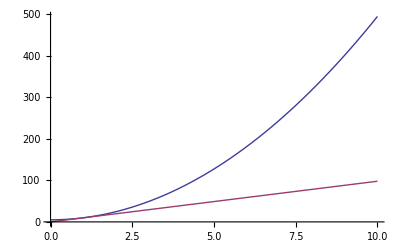

```mathematica
Plot[{yt,vt},{t,0,10}]
```

```mathematica
(*problem#2:Solve the differntial equation using the initial conditions at t=0,x=0,t=0,v=0,0.1*)
```

```mathematica
deq=x''[t]==p/(m*x'[t]);
sol=DSolve[deq,x[t],t]
```

{{x[t]→-(2 √2 m ((p t)/m+C[1])^(3/2))/(3 p)+C[2]},{x[t]→(2 √2 m ((p t)/m+C[1])^(3/2))/(3 p)+C[2]}}

```mathematica
xt=x[t]/.sol[[1]]
```

-(2 √2 m ((p t)/m+C[1])^(3/2))/(3 p)+C[2]

```mathematica
xt2=x[t]/.sol[[2]]/.{p->100,m->50}
```

1/3 √2 (2 t+C[1])^(3/2)+C[2]

```mathematica
vt=D[xt2,t]
```

√2 √(2 t+C[1])

```mathematica
eq1=(xt2/.t->0)==0
eq2=(vt/.t->0)==0
```

1/3 √2 C[1]^(3/2)+C[2]==0

√2 √C[1]==0

```mathematica
const=Solve[{eq1,eq2},{C[1],C[2]}]
```

{{C[1]→0,C[2]→0}}

```mathematica
xt2=xt2/.const[[1]]
vt=vt/.const[[1]]
```

(4 t^(3/2))/3

2 √t

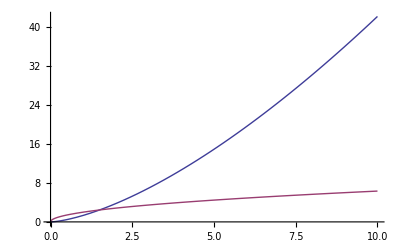

```mathematica
Plot[{xt2,vt},{t,0,10}]
```

```mathematica
(*problem#3:solve teh differential equation using the initial condition t=0,y=0,t=0,y'=1*)
```

```mathematica
deq=y''[t]+2y'[t]+y[t]==0;
sol=DSolve[deq,y[t],t]
```

{{y[t]→ⅇ^-t C[1]+ⅇ^-t t C[2]}}

```mathematica
yt=y[t]/.sol[[1]]
```

ⅇ^-t C[1]+ⅇ^-t t C[2]

```mathematica
vt=D[yt,t]
```

-ⅇ^-t C[1]+ⅇ^-t C[2]-ⅇ^-t t C[2]

```mathematica
eq1=(yt/.t->0)==0
eq2=(vt/.t->0)==1
```

C[1]==0

-C[1]+C[2]==1

```mathematica
const=Solve[{eq1,eq2},{C[1],C[2]}]
```

{{C[1]→0,C[2]→1}}

```mathematica
yt=yt/.const[[1]]
vt=vt/.const[[1]]
```

ⅇ^-t t

ⅇ^-t-ⅇ^-t t

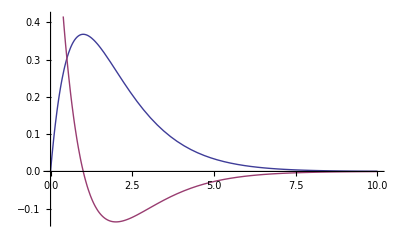

```mathematica
Plot[{yt,vt},{t,0,10}]
```